```mathematica
k
```

Moreover, all cells outside the boundary are dead.

So the condition for the whole object can be written as.

-Graphics-

```mathematica
life33
```

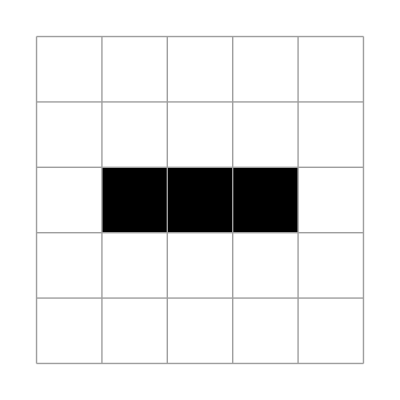

```mathematica
Clear[i,j,r,b,k];
(({{b[1,1], b[1,2], b[1,3], b[1,4], b[1,5]}, {b[2,1], b[2,2], b[2,3], b[2,4], b[2,5]}, {b[3,1], b[3,2], b[3,3], b[3,4], b[3,5]}, {b[4,1], b[4,2], b[4,3], b[4,4], b[4,5]}, {b[5,1], b[5,2], b[5,3], b[5,4], b[5,5]}})=(({{0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 1, 1, 1, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}})/.{1->True,0->False}))/.{True->1,False->0}//plt
```

```mathematica
lr
```

```mathematica
Get["stillLife`"]
```

```mathematica
neighborCount[{2},{2,2}]
```

True

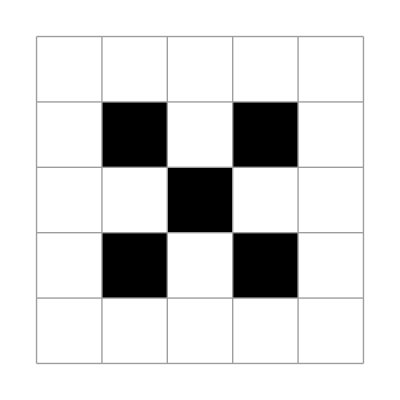

```mathematica
Clear[i,j];
b[0,_]=False;
b[_,0]=False;

b[_,6]=False;
b[6,_]=False;

Array[neighborCount[{2},{##}]&,{5,5}]//bool//plt
(*Array[{##}&,{5,5}]*)
```